# Sistemas Biológicos

## Práctica 1 - Modelos de una sola población

### 1

La ecuación

ẋ=r x(t)(1-(x(t-τ))/K)

Tiene 2 equilibrios: x = 0 y x=K. Reemplazando x = X+K queda

Ẋ=-r (X(t)(X(t-τ))/K+X(t-τ))

 y linealizando en torno a x=K  (X=0) obtenemos:
 
 Ẋ=-r X(t-τ)
 
 Buscamos soluciones de la forma X(t)=c ⅇ^λt para esta ecuación linealizada. Econtramos que para que esta sea solución, λ debe cumplir con
 
  λ +r ⅇ^-λτ=0
  
  En general, λ podría tomar cualquier valor complejo, por lo que reemplazamos λ = u + ⅈ v , y separamos parte real y parte imaginaria en la ecuación anterior. Obtenemos 2 ecuaciones (real e imaginaria):
  
  (u+ⅈ v) +r ⅇ^(-(u+ⅈ v)τ)=0→ Piecewise[{{u+r ⅇ^(-u τ)Cos(v τ), =0}, {v+r ⅇ^(-u τ)Sin  (v τ), =0}}]

#### Soluciones oscilatorias puras

Busquemos primero una solución que sea oscilatoria sostenida (u=0). En ese caso la ecuaciones nos quedan
  
    ⅈ v +r ⅇ^(-ⅈ v τ)=0→ Piecewise[{{Cos(v τ), =0}, {v+r Sin  (v τ), =0}}]→ {v τ = π/2+k π
v=(-1)^(k+1)r   para k∈Ζ
    
    Es decir, hemos encontrado que la condición que deben cumplir r y τ para que haya una solución oscilatoria pura es
    
    r τ = (π/2+k π)(-1)^(k+1)     para k∈Ζ
    
    y el correspondiente valor de λ para la solución propuesta será
    
     λ= ⅈ (-1)^(k+1)r      para k∈Ζ
     
     Pero, dado que r τ>0, debemos restringir los valores de k, así que finalmente nos queda
     
     r τ = (2k+1/2 )π     para k∈Ν
     y
     
      λ= ±ⅈ r

#### Soluciones monótonas

Busquemos ahora soluciones monótonas (v=0)  es decir λ = u  ∈ ℝ 

    u +r ⅇ^(-u τ)=0→ τ=(Log(-u/r))/-u
    
  La función (Log(-u/r))/-u tiene un máximo en u= -ⅇ r, en cuyo caso τ=1/(ϵ r). Es decir, se debe cumplir que r τ ≤1/ⅇ , de lo contrario no existiría solución para u en la ecuación. 
  Si se cumple  r τ ≤1/ⅇ , la ecuación tiene 2 soluciones:
  
     u_0=W_0(-r τ) /τ
  y
  
     u_-1=W_-1(-r τ) /τ
     
donde Wes la función W de Lambert.

#### Simulación

Hacemos una funcion para simular el modelo

```mathematica
sim[T_,k_,r_,f_,{a_,b_}]:=(
sol =n[t]/.First@NDSolve[{n'[t]== r n[t](1-n[t-T]/k),n[t /; t<0]==f[t]},n,{t,a T,b T}];
Plot[sol,{t,a T,b T},PlotRange->{0,All}]
)
```

En el siguiente gráfico puede observarse que existen regímenes oscilatorios, oscilatorios amortiguados y monótonos.

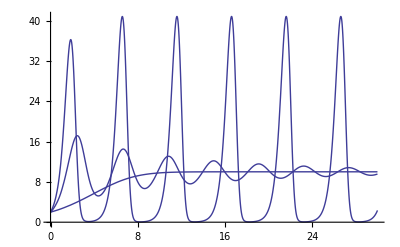

```mathematica
Show@@Table[sim[ 1,   10,r,(2&), {0,30}],{r,{1/ⅇ,0.9 π/2,1.5 π/2}}]
```

La transición de oscilatorio amortiguado a sostenido se da en r T=π/2

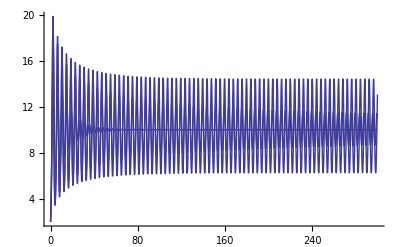

```mathematica
Show@@Table[sim[ 1,   10,r ,(2&), {0,300}],{r,{.9,1,1.02}π/2}]
```

Por otra parte, la transición de monótono a oscilatorio amortiguado esta en  r T=1/ⅇ

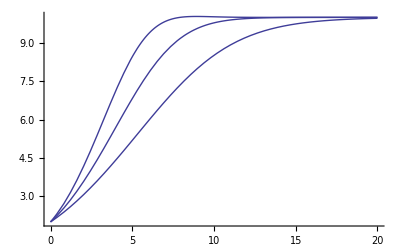

```mathematica
Show@@Table[sim[ 1,   10,r,(2&), {0,20}],{r,(1/ⅇ) +{-.1,0,.1}}]
```

### 2

En la simulación  siguiente podemos observar que la población subsiste pocas generaciones. La probabilidad que la población muera en una generación cualquiera es ⅇ^-1.7, por lo que la probabilidad de que no haya muerto en la generación n-esima es (1-ⅇ^-1.7)^n. La generación T en la que se extingue la población sigue una distribución de probabilidad P(n)=(1-ⅇ^-1.7)^n Log(1/(1-ⅇ^-1.7)) cuyo valor esperado es E(T)=4.95

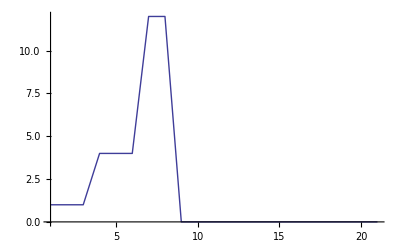

```mathematica
epochs=20;
r:=RandomVariate[PoissonDistribution[1.7],epochs];
realization= FoldList[#1*#2&,1,r];
ListPlot[realization,PlotRange->All,Joined->True]
```

### 3

La solución de la ecuación logistica es 

N(t)=K/(1+(K/N_0-1)ⅇ^(-r t))

De aquí se puede decir que, si la población luego de un desastre es N_i, la población luego del siguiente desastre, N_(i+1), que sucederá (en promedio) un tiempo 1/λ después, será

N_i=K/(1+(K/N_i-1)ⅇ^(-r /λ))

uno de los puntos fijos de este mapeo es N_0=0, el otro es

N_1=K (p-ⅇ^(-r/λ))/(1-ⅇ^(-r/λ))

para que N_1>0, se debe cumplir que

p>ⅇ^(-r/λ)

esta última es la condición que caracteriza la posibilidad del sistema de no extinguirse.

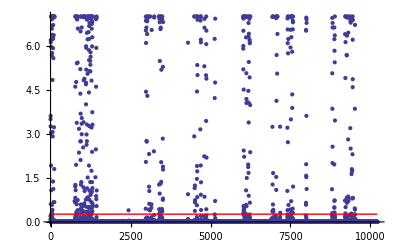

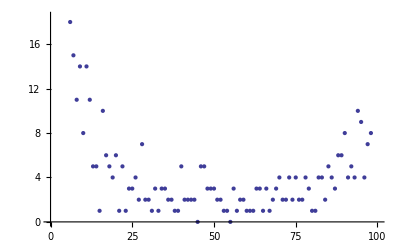

```mathematica
{k,p,r,λ} ={1000,.007,5,1};
n0 = k p/ 2; (*poblacion inicial*)
n1=k (p-ⅇ^(-r/λ))/(1-ⅇ^(-r/λ));
f[ni_,dt_]:=p k/(1+(k/ni-1)ⅇ^(-r dt))
t= RandomVariate[ExponentialDistribution[λ],10000];
n=FoldList[f,n0,t];
tt=FoldList[Plus,0,t];
Show[
ListPlot[MapThread[List,{tt,n}],PlotRange->{0,k p}],
Plot[n1,{time,First@tt,Last@tt},PlotStyle->{Red,Thick}]
]
ListPlot@BinCounts[n,{0,k p,k p/100}]
```

```mathematica
ⅇ^(-r/λ)1.
```

0.00673795

### 4 Efecto de Allee

Esta ecuación tiene 3 equilibrios, y ( para 0 <  A  < K ) se cumple que 

N_0=0 estable
N_1=A inestable
N_2=K estable

La logistica sólo tiene dos puntos de equilibrio (0 y K), y el punto N=0 es inestable, así que se cumple que N→ K cuando t→ ∞
En este modelo, N→ K si N(0)> A y N→ 0 si N(0)<A

### 5 Modelo Beverton Holt

Los puntos de equilibrio cumplen

	L=f(L)=(R_0 L)/(1+L/M)
De aquí se encuentra que tiene 2 puntos de equilibrio

	N_0= 0
	N_1=M (R_0-1)=K
	
Para analizar su estabilidad, evaluamos la derivada en N_0 y N_1

	f'(L)=(M^2 R_0)/(L+M)^2

	f'(N_0)=R_0

	f'(N_1)=R_0^-1

La condición para que un punto fijo L sea estable es que |f’(L)|<1, es decir que 

	N_0 Piecewise[{{estable, si |R_0|<1}, {inestable, si |R_0|>1}}]
	
	N_1 Piecewise[{{inestable, si |R_0|<1}, {estable, si |R_0|>1}}]

Esta ecuación es análoga a la logistica en el caso |R_0|>1, de tal manera que K > 1

## Práctica 2 - Poblaciones interactuantes

### 1 Control de plagas

Las suposiciones del modelo son:

-k N ( N+n) | → | Los fértiles compiten contra todos(N+n)por los recursos.
-b N  | → | mueren a una tasab
a N/(N+n)N | → | La tasa de reproducción es proporcional a la fracción de fértiles.Es decir,no distinguen con quien se reproducen

El modelo tiene 3 puntos fijos. Analicemos su estabilidad

(δ Ṅ)/(δ N)=-b+(a N (2 n+N))/(n+N)^2-k (n+2 N)
(δ Ṅ)/(δ N)|_(N=0)=-b-k n

```mathematica
FullSimplify@Solve[N(a N/(N+n)-b-k(N+n))==0,N]
```

{{N→0},{N→(a-b-2 k n+√((a-b)^2-4 a k n))/(2 k)},{N→-(-a+b+2 k n+√((a-b)^2-4 a k n))/(2 k)}}

```mathematica
FullSimplify@D[N(a N/(N+n)-b-k(N+n)),N]
```

-b+(a N (2 n+N))/(n+N)^2-k (n+2 N)

```mathematica
FullSimplify[-b+(a N (2 n+N))/(n+N)^2-k (n+2 N)/.{N->(a-b)/(2 k)- n±√(((a-b)/(2k))^2- (a n)/k)}]
```

k (2 (n±1/2 √(((a-b)^2-4 a k n)/k^2))+n (-1-(4 a k n)/((a-b+2 k n-2 k (n±1/2 √(((a-b)^2-4 a k n)/k^2)))^2)))

### 2 Competencia cíclica

Definiendo N = (n_1, n_2, n_3), A=(1 | α | β
β | 1 | α
α | β | 1), 𝟙=(1,1,1) y  * es el producto componente a componente, el sistema se puede escribir como
Ṅ= N* (𝟙-A.N)

Este sistema tiene 2 puntos fijos

N_0=0
N_1= A^-1. 𝟙=𝟙/(1+α+β)

Analicemos su estabilidad

(δ Ṅ)/(δ N)=Ι* (𝟙-A.N)-N*A

(δ Ṅ)/(δ N)|_(N=N_0)= Ι

(δ Ṅ)/(δ N)|_(N=N_1)= -A/(1+α+β)

Calculamos autovalores de las matrices

EigenValues(Ι)= (1,1,1) → N_0 inestable
EigenValues(-A/(1+α+β))=EigenValues(A)(-1/(1+α+β))= (-1,(((α+β)/2-1)±ⅈ(√3)/2(α-β))/(1+α+β))

El autovalor -1 de N_1 corresponde al autovector (1,1,1), por lo tanto es estable en esa dirección.
Los otros dos autovalores corresponden a espirales inestables (porque α+β>2 implica (α+β)/2-1>0)

Analizemos el comportamiento del sistema en el plano (que pasa por el punto fijo N_1)

 N.𝟙=3/(1+α+β)
 
 usando la transformación 
 
 N=T.X+𝟙/(1+α+β)
 
 con T=( 0 | 2/(√6) | 1/(√3)
1/(√2) | -1/(√6) | 1/(√3)
-1/(√2) | -1/(√6) | 1/(√3))
N* (𝟙-A.N)=-(T.X+𝟙/(1+α+β))* A. T.X

```mathematica
{1,1,1} ,{1,-1/2,-1/2} ,{0,1,-1}
```

```mathematica
-(( {{0, 2/(√6), 1/(√3)}, {1/(√2), -1/(√6), 1/(√3)}, {-1/(√2), -1/(√6), 1/(√3)}}).{x,y,0}+{1,1,1}/(1+α+β))* (({{1, α, β}, {β, 1, α}, {α, β, 1}}). ( {{0, 2/(√6), 1/(√3)}, {1/(√2), -1/(√6), 1/(√3)}, {-1/(√2), -1/(√6), 1/(√3)}}).{x,y,0})//FullSimplify
```

```mathematica
{((3 x (-α+β)+√3 y (-2+α+β)) (3+√6 y (1+α+β)))/(9 √2 (1+α+β)),((3 x (-1+α)+√3 y (1+α-2 β)) (6+3 √2 x (1+α+β)-√6 y (1+α+β)))/(18 √2 (1+α+β)),((√3 y (-1+2 α-β)+3 x (-1+β)) (-6+3 √2 x (1+α+β)+√6 y (1+α+β)))/(18 √2 (1+α+β))}
```

```mathematica
{Normalize@{1,-1/2,-1/2} ,Normalize@{0,1,-1}}
```

```mathematica
{{2/(√6),-1/(√6),-1/(√6)},{0,1/(√2),-1/(√2)}}
```

```mathematica
FullSimplify@Eigensystem[{{1, α, β}, {β, 1, α}, {α, β, 1}}(-1/(1+α+β))]
```

{{-1,(-2+α-√3 √(-(α-β)^2)+β)/(2 (1+α+β)),(-2+α+√3 √(-(α-β)^2)+β)/(2 (1+α+β))},{{1,1,1},{1/2 (-1+(√3 √(-(α-β)^2))/(α-β)),1/2 (-1+(√3 (α-β))/(√(-(α-β)^2))),1},{1/2 (-1+(√3 (α-β))/(√(-(α-β)^2))),1/2 (-1+(√3 √(-(α-β)^2))/(α-β)),1}}}

### 3 Destrucción de hábitat y coexistencia

La ecuación (0
0
0
h)=(ea y-ca x y+eb z-cb x z
y (-ea+ca x+ca z)
(-eb+cb x-ca y) z
x+y+z) tiene cuatro soluciones para X = (x
y
z)
X_0=(h
0
0), X_1=(ea/ca
h-ea/ca
0), X_2=(eb/cb
0
h-eb/cb), X_3=((eb+ca h-ea)/cb
h-ea/ca
ea/ca-(eb+ca h-ea)/cb)
El jacobiano del sistema es

J=(δ Ẋ)/(δ X)=(-ca y-cb z | ea-ca x | eb-cb x
ca y | -ea+ca x+ca z | ca y
cb z | -ca z | -eb+cb x-ca y)
Evaluando en los puntos fijos

J|_(X=X_0)=(0 | ea-ca h | eb-cb h
0 | ca h-ea | 0
0 | 0 | cb h-eb)

J|_(X=X_1)=(ea-ca h | 0 | eb-(cb ea)/ca
ca h-ea | 0 | ca h-ea
0 | 0 | ea+(cb ea)/ca-eb-ca h)
J|_(X=X_2)=(eb-cb h | ea-ca eb/cb | 0
0 | ca h-ea | 0
cb h-eb | ca (eb/cb-h) | 0)
J|_(X=X_3)=(-(cb ea)/ca+eb | ea-(ca (-ea+eb+ca h))/cb | ea-ca h
-ea+ca h | 0 | -ea+ca h
ea+(cb ea)/ca-eb-ca h | (-cb ea+ca (-ea+eb)+ca^2 h)/cb | 0)

```mathematica
({{1}, {y}, {z}})*(({{-ca x y-cb x z}, {0}, {0}})+({{0, ea, eb}, {ca, 0, ca}, {cb, -ca, 0}}).({{x}, {y}, {z}})-({{0}, {ea}, {eb}}))//MatrixForm
```

```mathematica
Solve[({{0}, {0}, {0}})==({{ea y-ca x y+eb z-cb x z}, {y (-ea+ca x+ca z)}, {(-eb+cb x-ca y) z}}),{x,y,z}]
```

{{x→ea/ca,z→0},{x→eb/cb,y→0},{y→0,z→0},{y→(-eb+cb x)/ca,z→(ea-ca x)/ca}}

```mathematica
Solve[{{0}, {0}, {0}}==({{1}, {y}, {z}})*(({{-ca x y-cb x z}, {0}, {0}})+({{0, ea, eb}, {ca, 0, ca}, {cb, -ca, 0}}).({{x}, {y}, {z}})-({{0}, {ea}, {eb}})),{x,y,z}]
```

{{x→ea/ca,z→0},{x→eb/cb,y→0},{y→0,z→0},{y→(-eb+cb x)/ca,z→(ea-ca x)/ca}}

```mathematica
FullSimplify@Inverse@({{0, ea, eb}, {ca, 0, ca}, {cb, -ca, 0}})
```

{{ca/(cb ea-ca eb),eb/(-cb ea+ca eb),ea/(cb ea-ca eb)},{cb/(cb ea-ca eb),(cb eb)/(ca (-cb ea+ca eb)),eb/(cb ea-ca eb)},{ca/(-cb ea+ca eb),(cb ea)/(ca cb ea-ca^2 eb),ea/(-cb ea+ca eb)}}

### 4 Metapoblaciones de presa y depredador

### 5 Ecuación de Fisher en dominios acotados

## Trabajo práctico 3

### 1

En una población de n individuos con una tasa de natalidad r en la que sólo hay nacimientos, el intervalo de tiempo δt que transcurrirá  hasta el próximo nacimiento es una variable aleatoria con una distribución exponencial con parámetro λ=r n.  La distribución exponencial tiene media μ= 1/λ=1/(r n) y varianza σ^2= 1/λ^2=1/(r n)^2

El tiempo t_n_f en que la población alcanza los n_f individuos es una variable aleatoria, que es la suma de los intervalos de tiempo entre los primeros n_f-n_0 nacimientos (siendo n_0 la población inicial). Es decir,

t_n_f=∑_(i=n_0)^(n_f-1) δt_i

De aquí podemos obtener la media μ y varianza σ^2 de t_n_f

μ | = | ∑_(i=n_0)^(n_f-1) 1/(r i) | = | (H_(n_f-1)-H_(n_0-1))/r

σ^2 | = | ∑_(i=n_0)^(n_f-1) 1/(r i)^2 | = | (H_(n_f-1)^(2)-H_(n_0-1)^(2))/r^2

Donde H_n^(r) es el n-ésimo número harmónico de orden r.  La relación entre la media μ y la varianza σ^2 de t_n_f con la población inicial n_0 puede verse explicitamente en las ecuaciones anteriores (a menor n_0, mayor μ y σ^2)

#### Simulación

Una función que nos permite realizar la simulación de t1000

```mathematica
tf[r_,n0_,nf_,fun_]:=Plus@@(fun/@ExponentialDistribution/@(r Range[n0,nf-1]))
```

Realizaremos la simulación para n_0={1,5,100}, n_f=1000 y r=1

```mathematica
{n0,nf,r}={{1,5,100},1000,1.};
```

Calculamos las medias y varianzas

```mathematica
Prepend[{#,tf[r,#,nf,Mean],tf[r,#,nf,Variance]}&/@n0,{"n_0","μ","σ^2"}]//Grid[#,Frame->All]&
```

n_0 | μ | σ^2
1 | 7.48447 | 1.64393
5 | 5.40114 | 0.220322
100 | 2.30709 | 0.00904967

Comparamos los resultados con los que econtramos teóricamente

```mathematica
Prepend[{#,(HarmonicNumber[nf-1]-HarmonicNumber[#-1])/r,(HarmonicNumber[nf-1,2]-HarmonicNumber[#-1,2])/r}&/@n0,{"n_0","μ","σ^2"}]//Grid[#,Frame->All]&
```

n_0 | μ | σ^2
1 | 7.48447 | 1.64393
5 | 5.40114 | 0.220322
100 | 2.30709 | 0.00904967

Hacemos histogramas realizando 1000 simulaciones para cada valor de n_0

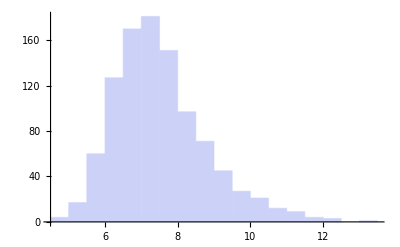
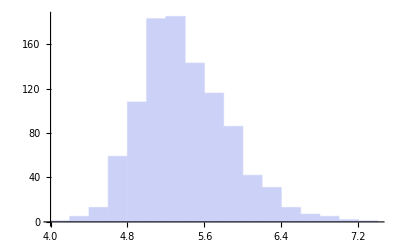
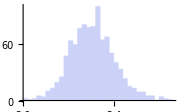
1 | -Graphics-
5 | -Graphics-
100 | -Graphics-

```mathematica
{#,Histogram@Table[tf[r,#,nf,RandomVariate],{i,1,1000}]}&/@n0//Grid
```

### 2

Analicemos el sistema

ẋ=x(1-x/k)-c x^2/(1+x^2)

```mathematica
(*Una función para graficar las raices de una expresión*)
BifurcationPlot[exp_,var_,paramRange_]:=Module[{
param=paramRange[[1]],
roots=Solve[exp==0,var],
dexp=D[exp,var],
p,dp,stable,unstable,plot},(
p  =(  var/.#)&/@roots;
dp=(dexp/.#)&/@roots;
stable    =MapThread[If[(Re[#1]<0),#2,ⅈ]&,{dp,p}];
unstable=MapThread[If[(Re[#1]>0),#2,ⅈ]&,{dp,p}];
Show[
Plot[stable    ,paramRange,PlotRange->All,Axes->False,Frame->True,PlotStyle->{{Black,Thick}}    ],
Plot[unstable,paramRange,PlotRange->All,Axes->False,Frame->True,PlotStyle->{{Black,Thick,Dashed}}]]
)]
```

Veamos cómo van cambiando los puntos fijos con c para distintos valores de k

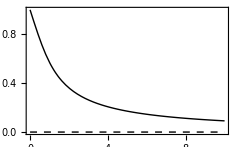
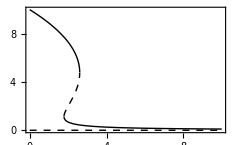
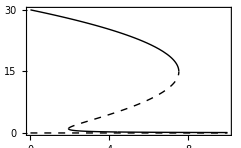
-Graphics- | -Graphics- | -Graphics-
1 | 10 | 30

```mathematica
Table[{BifurcationPlot[x(1-x/k)-c x^2/(1+x^2),x,{c,0,10}],k},{k,{1,10,30}}]//Transpose//Grid
```

Independientemente del valor de k, x_0=0 es un punto fijo inestable del sistema.
Además, vemos que para k chico hay un punto fijo x_1 que es estable, que sigue existiendo para todo valor de c (en el caso particular c=0, x_1=k).
Cuando aumentamos el valor de k aparecen dos puntos fijos nuevos x_2 (inestable) y x_3 (estable). Para c chicos, hay un solo punto fijo estable, x_1.
x_2 y x_3 aparecen a partir de cierto valor crítico de c, y comenzamos a tener 2 puntos fijos estables. Si seguimos aumentando c, x_1 y x_2 desaparecen, quedando sólo el punto fijo x_3.

Si se parte de un c pequeño y se va incrementeando su valor lentamente, el sistema se desplazará por el punto fijo x_1. Cuando se alcanze el valor crítico de c en el que x_1 deja de existir, el sistema se irá al punto fijo estable x_3. Si ahora disminuímos lentamente el valor de c, el sistema se desplazará por el x_3, hasta llegar al valor en que x_3 deja de existir. Acanzado este valor de c, el sistema se irá al punto fijo x_1. Es decir, se produce un fenomeno de histéresis.

### 3

Implementamos el algoritmo de Gillespie para el sistema dado

```mathematica
GillespieSim[N0_,b_,d_,epochs_]:=(
fN[N_]:=If[N>0,N+RandomChoice[{b N,d N(N-1)/2}-> {1,-2}],0];
fT[N_]:=If[N>0,RandomVariate@ExponentialDistribution[b N+d N(N-1)/2],0];
nlist = NestList[fN,N0,epochs];
tlist=Most@Accumulate@Prepend[fT/@nlist,0];
(*tlist=Most@FoldList[#1+fT@#2&,0,nlist];*)
{tlist,nlist}
)
```

Elegimos b= 0.3 y d=0.1 y hacemos un histograma con los tiempos de extincion para multiples realizaciones

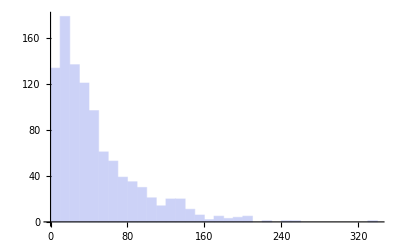

```mathematica
extincionT:=If[#2==0,#1,ⅈ]&@@Last@Transpose@GillespieSim[30,.3,.1,1000]
Histogram@Table[extincionT,{i,0,1000}]
```

Elegimos b= 0.3 y d=0.01 y hacemos multiples realizaciones para obtener la distribución estacionaria

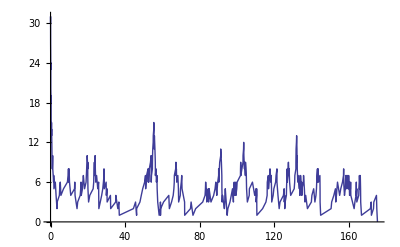

```mathematica
ListPlot[Transpose@GillespieSim[30,.3,.1,1000],PlotRange->{0,Max@nlist},Joined->True]
```

### 4

## Trabajo práctico 4

### 1

Analicemos el sistema

ṗ=(ẋ
ẏ)=(-x+a y+x^2 y
b-a y-x^2 y)

Este sistema tiene un sólo punto fijo

p_0=(x_0
y_0)=(b
b/(a+b^2))

El Jacobiano de este sistema evaluado en el punto fijo es

(δ ṗ)/(δ p)|_(p=p_0)=(-1+2 x y | a+x^2
-2 x y | -a-x^2)|_(p=p_0)=(-1+(2 b^2)/(a+b^2) | a+b^2
-(2 b^2)/(a+b^2) | -a-b^2)

Si calculamos los autovalores de este sistema y pedimos que su parte real sea positiva (para que sea un punto fijo inestable), llegamos a la condición para a y b

a-b^2+(a+b^2)^2<0

Puede comprobarse que el flujo en la región acotada por las 4 rectas

y=b/a | 0<x<b
x+y=b+b/a | b<x<b+b/a
y=0 | 0<x<b+b/a
x=0 | 0<y<b/a

es sólo entrante (para cualquier valor de b y a).

Dado que las trayectorias en el contorno de esta región son sólo entrantes, y que el punto fijo en su interior es inestable, debe existir un cíclo límite.

En el siguiente gráfico ( para a=.1 y b=.5 ) pueden verse las nulclinas en rojo, y la manera en la que fluyen las trayectorias. Una de las trayectorias que se aproxima al ciclo limite se ve en naranja.

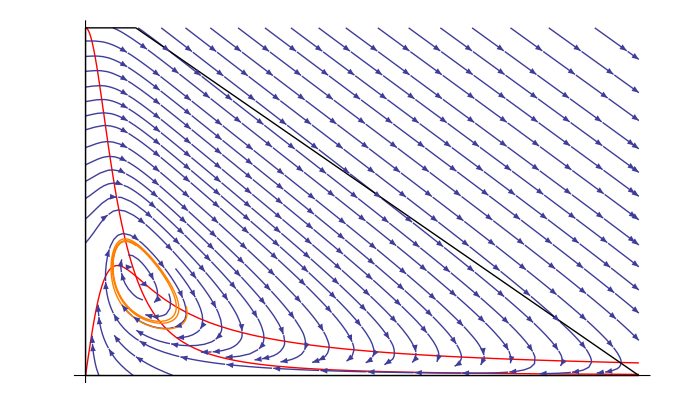

```mathematica
{a,b}={.1,.5};
sol=First@NDSolve[{x'[t]==-x[t]+a y[t]+x[t]^2 y[t],y'[t]==b-a y[t]-x[t]^2 y[t],x[0]== 1,y[0]== 1},{x,y},{t,0,30}];
Show[
Plot[{x/(a+x^2),b/(a+x^2)},{x,-.01,b+b/a+0.01},PlotRange->All,Ticks->False,PlotStyle->{{Red,Thick}}],
StreamPlot[{-x+a y+x^2 y,b-a y-x^2 y},{x,-.01,b+b/a+0.01},{y,-.01,b/a+.01},Frame-> False],
ContourPlot[y== b/a,{x,0,b},{y,-.01,b/a+.01},ContourStyle->{Black,Thick} ],
ContourPlot[x+y== b+b/a,{x,b,b+b/a},{y,-.01,b/a+.01},ContourStyle->{Black,Thick} ],
ContourPlot[y==0,{x,-.01,b+b/a+0.01},{y,-.01,b/a+.01},ContourStyle->{Black,Thick} ],
ContourPlot[x==0,{x,-.01,b+b/a+0.01},{y,-.01,b/a+.01},ContourStyle->{Black,Thick} ],
ParametricPlot[{x[t],y[t]}/.sol,{t,0,30},PlotStyle->{Orange,Thick}]
]
Clear[a]
Clear[b]
```

### 2

```mathematica
Solve[{0== a-Sin[θ1]+k Cos[θ2-θ1],0==a+Sin[θ2]+k Cos[θ1-θ2]},{θ1,θ2}]
```

### 3

## Práctico 5